```mathematica
phDist=res[[2,1,;;]];
Manipulate[ListDensityPlot[Join[#[[1]],{#[[2]]}]&/@Transpose[{xpGrid,phDist[[i]]}],PlotRange->All,PlotLegends->Automatic],{i,1,Length[phDist],1}]
```

```mathematica
ListDensityPlot[Join[#[[1]],{#[[2]]}]&/@Transpose[{xpGrid,res[[26,1,-1]]-res[[2,1,-1]]}],{PlotRange->All,PlotLegends->Automatic}]
```

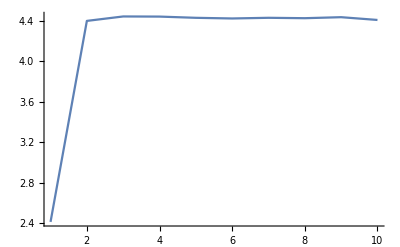

```mathematica
ent[plis_]:=-Total[# Log[#+10.^-10]&/@plis];
ListLinePlot[ent/@res[[10,1,;;]],PlotRange->All]
```

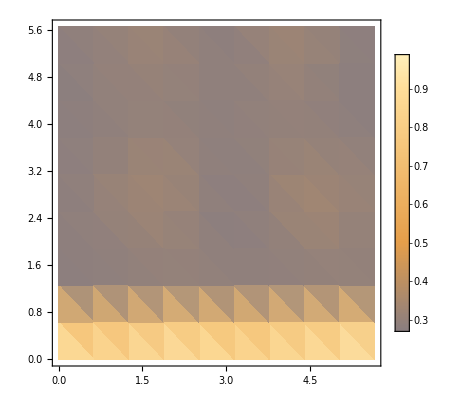

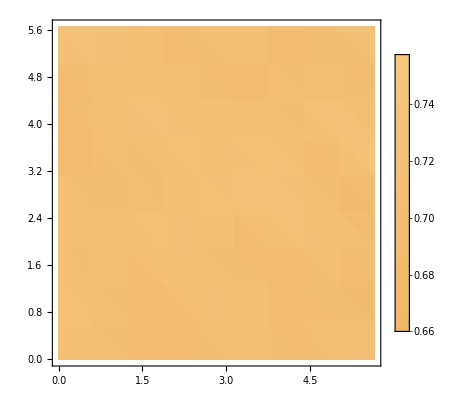

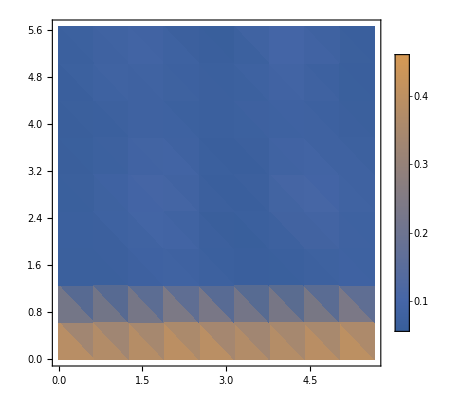

```mathematica
SetDirectory["/home/leonard/Documents/Projects/PhysicalDistance/Codes/data/KickedRotor/"];
k=10.1;
m=10;
prefix="K="<>ToString[k]<>"_m="<>ToString[m];
savdSet=Import[prefix<>"/tLis.dat","Table"]//Flatten;
len=Length[savdSet];
tabs=Import[prefix<>"/GrossTabs.txt","Table"];
stattabs=Import[prefix<>"/GrossStatTabs.txt","Table"];
qavtab=Import[prefix<>"/qAVtab.txt","Table"];
qtabs=Table[Flatten[{#[[1;;2]],(#[[2+i]])/Max[tabs[[;;,2+i]]]}]&/@tabs,{i,1,len}];
ftabs=Table[Flatten[{#[[1;;2]],(#[[2+len+i]])/Max[tabs[[;;,2+len+i]]]}]&/@tabs,{i,1,len}];
qtab=Mean[qtabs];
ftab=Mean[ftabs];
qstatTabs=Table[#[[i]]&/@stattabs,{i,1,len}];
klstatTabs=Table[#[[i+3len]]&/@stattabs,{i,1,len}];
fklstatTabs=Table[#[[i+2len]]&/@stattabs,{i,1,len}];
ListDensityPlot[qtab,{PlotRange->All,ColorFunctionScaling->False,PlotLegends->Automatic}]
ListDensityPlot[ftab,{PlotRange->All,ColorFunctionScaling->False,PlotLegends->Automatic}]
ListDensityPlot[qavtab,{PlotRange->All,ColorFunctionScaling->False,PlotLegends->Automatic}]
```

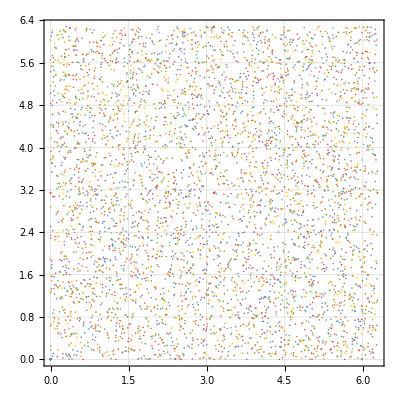

```mathematica
ListPlot[res[[;;,3]],{PlotTheme->"Detailed",AspectRatio->1}]
```

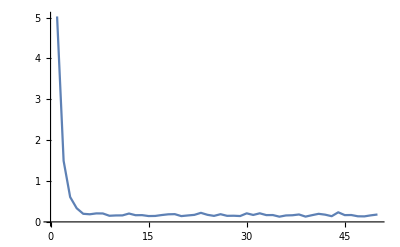

```mathematica
ListLinePlot[qstatTabs[[;;,-1]],PlotRange->All]
```

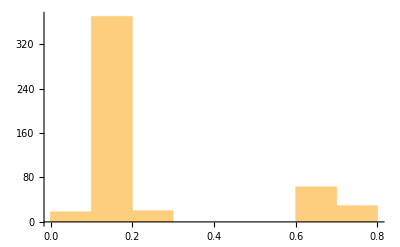

```mathematica
Histogram[qstatTabs[[-1]]]
```

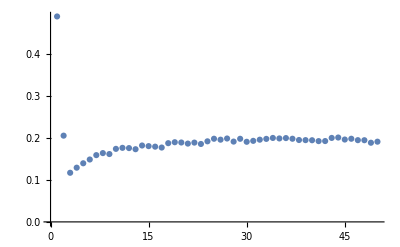

```mathematica
ListPlot[(Variance/@qstatTabs)/(Mean/@qstatTabs),PlotRange->All]
```

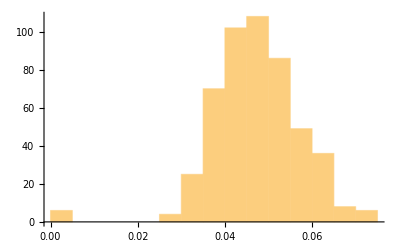

```mathematica
Histogram[klstatTabs[[-1]]]
```

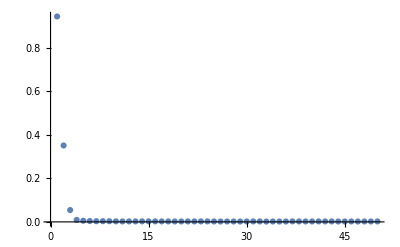

```mathematica
ListPlot[(Variance/@klstatTabs)/(Mean/@klstatTabs),PlotRange->All]
```

```mathematica
ListPlot3D[Partition[res[[4,1,3]],m],PlotRange->All]
```

-Graphics3D-

```mathematica
klD[p1_,p2_]:=Total[p1*Log[(p1+10.^-6)/(p2+10^-6)]]
```

```mathematica
klD[res[[9,1,-1]],res[[-1,1,-1]]]
```

0.0375291

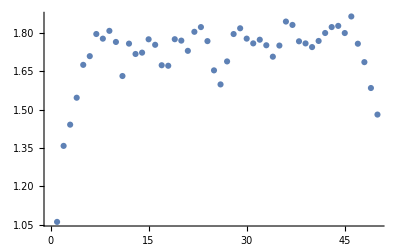

```mathematica
ListPlot[Table[Variance[#]/Mean[#]&[Flatten[Table[klD[res[[i,1,t]],res[[j,1,t]]],{i,1,Length[grdLabs]},{j,i+1,Length[grdLabs]}]]],{t,1,Length[savdSet]}],PlotRange->All]
```